```mathematica
(*I call my lorentz boosts L and LL(inverse) for a little while, then switch to Λ and Λp(inverse)*)
```

```mathematica
Remove["Global`*"];
	
(*make the lorentz boost:*)
L={{γ,γ β, 0, 0}, {γ β, γ ,0,0},{0,0,1,0},{0,0,0,1}};
LL=Inverse[L];
r={c t,x,y,z};
r'={c t',x',y',z'};


Print["The Lorentz boost ( from rocket frame to lab frame) : L= ",L//MatrixForm//Simplify]
Print["The Inverse Operator (from lab frame to rocket frame): L'= ",LL//MatrixForm//FullSimplify]

γ=1/√(1-β^2);
β=v/c;

Print["\n Mapping from rocket frame to to lab frame, we get:"]
Print["r=L.r'=", L.r'//MatrixForm//Simplify]

Print["\n Mapping from lab frame to to rocket frame, we get:"]
Print["r'=L'.r= ",LL.r//MatrixForm//Simplify]

Print["\nThis is the same as swapping the primes and changing the direction of velocity. In the rocket frame (S') we see (S) moving backwards at v, and the converse when in the lab frame"]
```

The Lorentz boost ( from rocket frame to lab frame) : L= (γ | β γ | 0 | 0
β γ | γ | 0 | 0
0 | 0 | 1 | 0
0 | 0 | 0 | 1)

The Inverse Operator (from lab frame to rocket frame): L'= (1/(γ-β^2 γ) | β/((-1+β^2) γ) | 0 | 0
β/((-1+β^2) γ) | 1/(γ-β^2 γ) | 0 | 0
0 | 0 | 1 | 0
0 | 0 | 0 | 1)

Mapping from rocket frame to to lab frame, we get:

r=L.r'=((c^2 t'+v x')/(c √(1-v^2/c^2))
(v t'+x')/(√(1-v^2/c^2))
y'
z')

Mapping from lab frame to to rocket frame, we get:

r'=L'.r= ((c^2 t-v x)/(c √(1-v^2/c^2))
(-t v+x)/(√(1-v^2/c^2))
y
z)

This is the same as swapping the primes and changing the direction of velocity. In the rocket frame (S') we see (S) moving backwards at v, and the converse when in the lab frame

```mathematica
Remove["Global`*"];
$Assumptions={Element[{γ,β,c,t,t',θ',ϕ'},Reals]&& γ≥0 &&0≤β≤1 &&c>0 &&t>0&&t'≥ 0};

L={{γ,γ β, 0, 0}, {γ β, γ ,0,0},{0,0,1,0},{0,0,0,1}};
LL=Inverse[L];

γrule=γ->1/√(1-β^2);
r'={c t',c t' Cos[θ'] ,c t' Sin[θ']Sin[ϕ'], c t' Cos[ϕ']  Sin[θ'] };
Print["The event describing the photon in the rocket frame is r'=", r'//MatrixForm]

r=L.r'/.γrule;



Print["\n Mapping from rocket frame to to lab frame, we get:"]
Print["r=L.r'=", r//MatrixForm//Simplify]


dist=√(r.r-r[[1]]^2)//Refine//Simplify;
time=r [[1]]/c //Simplify;
speed=dist/time//Simplify
```

The event describing the photon in the rocket frame is r'=(c t'
c Cos[θ'] t'
c Sin[θ'] Sin[ϕ'] t'
c Cos[ϕ'] Sin[θ'] t')

Mapping from rocket frame to to lab frame, we get:

r=L.r'=((c (1+β Cos[θ']) t')/(√(1-β^2))
(c (β+Cos[θ']) t')/(√(1-β^2))
c Sin[θ'] Sin[ϕ'] t'
c Cos[ϕ'] Sin[θ'] t')

c

```mathematica
Remove["Global`*"];

$Assumptions={Element[{γ,β,c,t,t',θ',ϕ',δtp},Reals]&& γ≥0 &&0≤β≤1 &&c>0 &&t>0&&t'≥ 0&&δtp>0};
L={{γ,γ β, 0, 0}, {γ β, γ ,0,0},{0,0,1,0},{0,0,0,1}};
LL=Inverse[L];

(*two events in rocket frame*)
r1p={c t1p,x1p,y1p,z1p};
r2p={c t2p,x2p,y2p,z2p};

(*colocated events in rocket frame*)
x1p=x2p;
y1p=y2p;
z1p=z2p;
Δt=((L.r2p)[[1]] - (L.r1p)[[1]])/c //Simplify;
Print["In the lab frame, we see the time between the two events which are co-located in the rock frame as Δt= ", Δt]

(*Simultanious events in rocket frame*)
x1p:=x1p;
y1p:=y1p;
z1p:=z1p;
t1p:=t2p;
r1=L.r1p;
r2=L.r2p;
Δr=r2-r1//Simplify;
cΔt=Δr[[1]];
Print["\nIn lab frame, the time between two events which are simultanious in he rocket frame is Δt= ", cΔt/c//Simplify//MatrixForm]




(*length contraction*)

βrule=Solve[γ==1/√(1-β^2),β][[2]];
δrp={c δtp, dp,0,0};
δr={0,d,0,0};
δrtemp=L.δrp/.βrule;
soln=Solve[{δrtemp[[1]]==δr[[1]],δrtemp[[2]]==δr[[2]]},{d,δtp}][[1]];

Print["\nIn the rocket, we measure dp. In the lab, we measure ", d/.soln]
```

In the lab frame, we see the time between the two events which are co-located in the rock frame as Δt= (-t1p+t2p) γ

In lab frame, the time between two events which are simultanious in he rocket frame is Δt= ((-x1p+x2p) β γ)/c

In the rocket, we measure dp. In the lab, we measure dp/γ

```mathematica
Remove["Global`*"];

$Assumptions={Element[{γ,β,c,δtp},Reals]&& γ≥0 &&0≤β≤1 &&c>0&&δtp>0};

Λ={{γ,γ β, 0, 0}, {γ β, γ ,0,0},{0,0,1,0},{0,0,0,1}};


γrule=γ->1/√(1-β^2);
βrule=Solve[γ==1/√(1-β^2),β][[2]];
β=vx/c;

(*in the rocket*)
δrp={c δtp,δxp , δyp , 0};
δxp=u δtp Cos[θp];
δyp=u δtp Sin[θp];
δtp=L/u;
(*the time it takes to rover to move up the ramp in the ship*)

(*at the space station*)

δr=Λ.δrp;

δt=δr[[1]]/c/.γrule //Simplify;
Print["At the space station, we measure the time it takes to rover to travel up the ramp to be ", δt];
(************)
Clear[δtp]
δrp={c δtp,L Cos[θp],L Sin[θp], 0};
δr={c δt,d Cos[θ], d Sin[θ],0};
δrtemp=Λ.δrp;
soln=Solve[{δr[[1]]==δrtemp[[1]],δr[[2]]^2+δr[[3]]^2== δrtemp[[2]]^2+δrtemp[[3]]^2},{δtp,d}][[2]]/.γrule//FullSimplify;

Print["\nOn the space station, we see the rover travel a length", d/.soln]
(***********)
(* velocity from my space station*)
Clear[δt]
δrp={c δtp,uxp δtp,uyp δtp,uzp δtp};
δr=Λ.δrp;
δrtemp={c δt, ux δt, uy δt, uz δt};
uxp=u Cos[θp];
uyp=u Sin[θp];
uzp=0;

eqnlist={δr[[1]]==δrtemp[[1]], δr[[2]]==δrtemp[[2]],δr[[3]]==δrtemp[[3]],δr[[4]]==δrtemp[[4]]};
slist={δt,ux,uy,uz};
soln=Solve[eqnlist,slist];

ulab={δt/.soln,ux/.soln,uy/.soln,uz/.soln}//Simplify;
Print["\nOn the space station, we measure the velocity of the rover to be", ulab/.γrule//Simplify//MatrixForm]

(***************)
(*Length of ramp in the ship*)
Clear[δtp]
δrp={c δtp,L Cos[θp],L Sin[θp], 0};
δr={0,d Cos[θ], d Sin[θ],0};
δrtemp=Λ.δrp;

soln=Solve[{δr[[1]]==δrtemp[[1]],δr[[2]]^2+δr[[3]]^2== δrtemp[[2]]^2+δrtemp[[3]]^2},{δtp,d}][[2]]/.γrule//FullSimplify//TrigReduce;

Print["\nIn the space station, we measure the ramp to be ",d/.soln ,"This is not the same as the distance we see the rover travel since ,we measure the ramp as a single simultanious measurement. If we measure the length the rover travels, that is two events separated by the time we see the rover start moving and when we see it stop moving."]
```

At the space station, we measure the time it takes to rover to travel up the ramp to be (L (c^2+u vx Cos[θp]))/(c u √(c^2-vx^2))

On the space station, we see the rover travel a length(√((L^2 (-u^2 vx^2+2 c^2 (u^2+vx^2)+u vx (4 c^2 Cos[θp]+u vx Cos[2 θp])))/(u^2 (c-vx) (c+vx))))/(√2)

On the space station, we measure the velocity of the rover to be((c δtp (1+(u vx Cos[θp])/c^2))/(√(c^2-vx^2))
(c^2 (vx+u Cos[θp]))/(c^2+u vx Cos[θp])
(c u √(c^2-vx^2) Sin[θp])/(c^2+u vx Cos[θp])
0)

In the space station, we measure the ramp to be (L √(2 c^2-vx^2-vx^2 Cos[2 θp]))/(√2 c)This is not the same as the distance we see the rover travel since ,we measure the ramp as a single simultanious measurement. If we measure the length the rover travels, that is two events separated by the time we see the rover start moving and when we see it stop moving.

```mathematica
Remove["Global`*"];

Λ={{γ,γ β, 0, 0}, {γ β, γ ,0,0},{0,0,1,0},{0,0,0,1}};
(*event in rocket frame*)
δrp={c δtp,uxp δtp,uyp δtp,uzp δtp};
Print["we shoot with velocity vector u. the event looks like δrp= ", δrp//MatrixForm]
(*boost to lab*)
δr=Λ.δrp;
Print["In the lab, the even looks like δr= ", δr//MatrixForm];

δr0={c δt, ux δt, uy δt, uz δt};

eqnlist={δr[[1]]==δr0[[1]], δr[[2]]==δr0[[2]],δr[[3]]==δr0[[3]],δr[[4]]==δr0[[4]]};
slist={δt,ux,uy,uz};
soln=Solve[eqnlist,slist][[1]];
ulab={δt/.soln,ux/.soln,uy/.soln,uz/.soln}//Simplify;

Print["In the lab, we see the velocity vector as u=", ulab//MatrixForm]
```

we shoot with velocity vector u. the event looks like δrp= (c δtp
uxp δtp
uyp δtp
uzp δtp)

In the lab, the even looks like δr= (c γ δtp+uxp β γ δtp
uxp γ δtp+c β γ δtp
uyp δtp
uzp δtp)

In the lab, we see the velocity vector as u=(((c+uxp β) γ δtp)/c
(c (uxp+c β))/(c+uxp β)
(c uyp)/(c γ+uxp β γ)
(c uzp)/(c γ+uxp β γ))

```mathematica
Remove["Global`*"];
Λ={{γ,γ β, 0, 0}, {γ β, γ ,0,0},{0,0,1,0},{0,0,0,1}};
(*4 inner product*)
dot4[u_,v_]=2(u[[1]] v[[1]])-u.v;//Quiet
A={at, ax,ay,az};
B={bt, bx,by,bz};
A'={at',ax',ay',az'};
B'={bt', bx',by',bz'};
Atemp=Λ.A';
Btemp=Λ.B';
γrule=γ->1/√(1-β^2);


eqnlist={Atemp[[1]]== A[[1]],Atemp[[2]]==A[[2]],Atemp[[3]]==A[[3]],Atemp[[4]]== A[[4]],Btemp[[1]]==B[[1]],Btemp[[2]]==B[[2]],Btemp[[3]]==B[[3]],Btemp[[4]]==B[[4]]};
solist={at',ax',ay',az',bz',bt',bx',by'};
soln=Solve[eqnlist,solist];

dot4[A',B']/.soln[[1]]/.γrule//Simplify
(*QED*)


(***************)
P={En/c, Px,Py,Pz};

dot4[P,P]

(*******************)
Pt=γ m c;
βrule=β->u/c;
γ=1/√(1-β^2);

expand=Series[Pt,{β,0,4}];
expand/.βrule//Quiet
```

at bt-ax bx-ay by-az bz

En^2/c^2-Px^2-Py^2-Pz^2

c m+1/2 c m (u/c)^2+3/8 c m (u/c)^4+O[u/c]^5

Before Transformation:

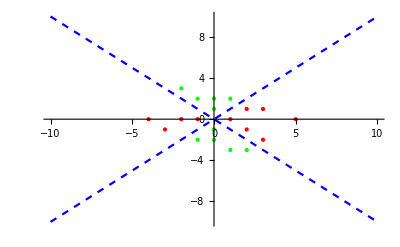

After Transformation:

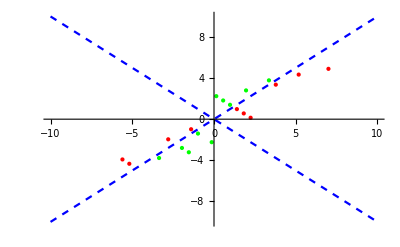

```mathematica
Remove["Global`*"];

Λ={{γ,γ β}, {γ β, γ }};

γ1:=Plot[x,{x,-10,10},PlotStyle->{Blue,Dashed}]
γ2:=Plot[-x,{x,-10,10},PlotStyle->{Blue,Dashed}]
inpts:={{0,1},{0,2},{1,2},{-1,2},{-1,-2},{0,-1},{0,-2},{2,-3},{1,-3},{-2,3}}
outpts:={{1,0},{-1,0},{-2,0},{2,1},{2,-1},{-3,-1},{-4,0},{3,1},{5,0},{3,-2}}
	
S=Show[γ1,γ2,Graphics[{PointSize[Medium],Green,Point[inpts]}],Graphics[{PointSize[Medium],Red,Point[outpts]}]];
Print["\nBefore Transformation:"]
Print[S]

γ=1/√(1-β^2);
β=.7;
inptsP=Table[Λ.inpts[[i]],{i,1,10}];
outptsP=Table[Λ.outpts[[i]],{i,1,10}];
Sp=Show[γ1,γ2,Graphics[{PointSize[Medium],Green,Point[inptsP]}],Graphics[{PointSize[Medium],Red,Point[outptsP]}]];
Print["\nAfter Transformation:"]
Print[Sp]

(*I couldnt ever get my ct line to plot*)
```